{{d→InterpolatingFunction[{{0.,60.}},<>],c→InterpolatingFunction[{{0.,60.}},<>],x→InterpolatingFunction[{{0.,60.}},<>],m→InterpolatingFunction[{{0.,60.}},<>],a→InterpolatingFunction[{{0.,60.}},<>]}}

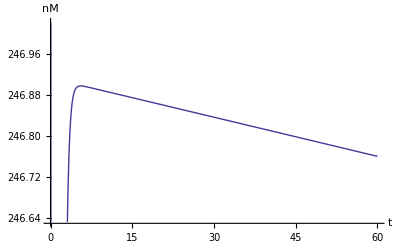

```mathematica
sol1=NDSolve[{d'[t]==0.0000926*d[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.00000000005*x[t]*d[t]-.0005*m[t]*d[t], x'[t]== 10000+.0000926*x[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.09*x[t]*d[t]-.09*x[t]*m[t],m'[t]==0.0000339*m[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.00000000005*x[t]*m[t]-.005*m[t]*d[t],c'[t]==  0.000227*c[t](1-(c[t]/1000)),a'[t]== 0.0001135*a[t]*(1-(a[t]/1000)), d[0]==500,c[0]==500,x[0]==10000,m[0]==500,a[0]==500},{d,c,x,m,a},{t,0,60}]

Plot[Evaluate[{x[t]}/.sol1],{t,0,60},AxesLabel->{t,nM}]
```

{{d→InterpolatingFunction[{{0.,4320.}},<>],c→InterpolatingFunction[{{0.,4320.}},<>],m→InterpolatingFunction[{{0.,4320.}},<>],a→InterpolatingFunction[{{0.,4320.}},<>]}}

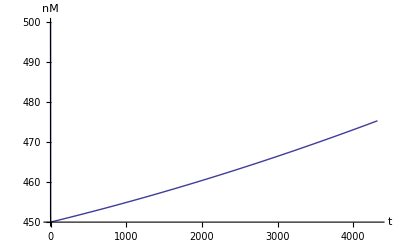

```mathematica
sol1=NDSolve[{d'[t]==0.0000926*d[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.0005*m[t]*d[t], m'[t]==0.0000339*m[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.005*m[t]*d[t],c'[t]==  0.000227*c[t](1-(c[t]/1000)),a'[t]== 0.0001135*a[t]*(1-(a[t]/1000)), d[0]==500,c[0]==500,m[0]==500,a[0]==500},{d,c,m,a},{t,0,4320}]

Plot[Evaluate[{d[t]}/.sol1],{t,0,4320},AxesLabel->{t,nM}]
```

{{c→InterpolatingFunction[{{0.,24000.}},<>],x→InterpolatingFunction[{{0.,24000.}},<>],m→InterpolatingFunction[{{0.,24000.}},<>],a→InterpolatingFunction[{{0.,24000.}},<>]}}

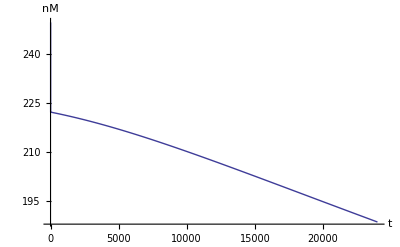

```mathematica
sol1=NDSolve[{ x'[t]== 10000+.0000926*x[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.09*x[t]*m[t],m'[t]==0.0000339*m[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.00000000005*x[t]*m[t],c'[t]==  0.000227*c[t](1-(c[t]/1000)),a'[t]== 0.0001135*a[t]*(1-(a[t]/1000)),c[0]==500,x[0]==10000,m[0]==500,a[0]==500},{c,x,m,a},{t,0,24000}]

Plot[Evaluate[{x[t]}/.sol1],{t,0,24000},AxesLabel->{t,nM}]
```

{{d→InterpolatingFunction[{{0.,24000.}},<>],c→InterpolatingFunction[{{0.,24000.}},<>],x→InterpolatingFunction[{{0.,24000.}},<>],a→InterpolatingFunction[{{0.,24000.}},<>]}}

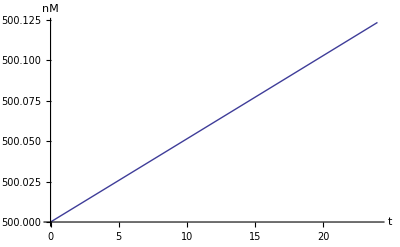

```mathematica
sol1=NDSolve[{d'[t]==0.0000926*d[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.00000000005*x[t]*d[t], x'[t]== 10000+.0000926*x[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.09*x[t]*d[t],c'[t]==  0.000227*c[t](1-(c[t]/1000)),a'[t]== 0.0001135*a[t]*(1-(a[t]/1000)), d[0]==500,c[0]==500,x[0]==10000,a[0]==500},{d,c,x,a},{t,0,24000}]

Plot[Evaluate[{d[t]}/.sol1],{t,0,24},AxesLabel->{t,nM}]
```

{{d→InterpolatingFunction[{{0.,4320.}},<>],c→InterpolatingFunction[{{0.,4320.}},<>],m→InterpolatingFunction[{{0.,4320.}},<>],a→InterpolatingFunction[{{0.,4320.}},<>],p→InterpolatingFunction[{{0.,4320.}},<>]}}

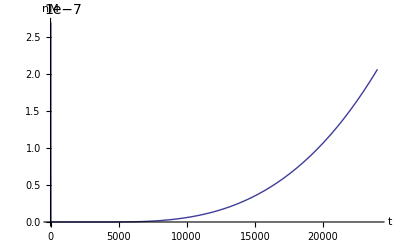

```mathematica
sol1=NDSolve[{d'[t]==0.0000926*d[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.0005*m[t]*d[t]-.005*p[t]*d[t], m'[t]==0.0000339*m[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.005*m[t]*d[t]-.0005*p[t]*m[t],c'[t]==  0.000227*c[t](1-(c[t]/1000)),a'[t]== 0.0001135*a[t]*(1-(a[t]/1000)),p'[t]== 0.0000339*p[t]*(a[t]/(1000+a[t]))-.005*p[t]*m[t]-.005*p[t]*d[t],d[0]==500,c[0]==500,m[0]==500,a[0]==500,p[0]==500},{d,c,m,a,p},{t,0,4320}]

Plot[Evaluate[{p[t]}/.sol1],{t,0,24000},AxesLabel->{t,nM}]
```

{{d→InterpolatingFunction[{{0.,24000.}},<>],c→InterpolatingFunction[{{0.,24000.}},<>],x→InterpolatingFunction[{{0.,24000.}},<>],m→InterpolatingFunction[{{0.,24000.}},<>],a→InterpolatingFunction[{{0.,24000.}},<>],p→InterpolatingFunction[{{0.,24000.}},<>]}}

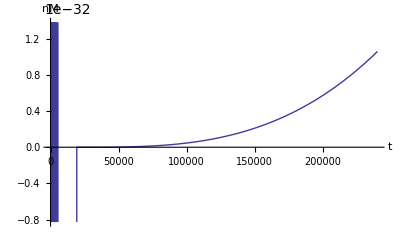

```mathematica
sol1=NDSolve[{d'[t]==0.0000926*d[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.00000000005*x[t]*d[t]-.0005*m[t]*d[t], x'[t]== 10000+.0000926*x[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.09*x[t]*d[t]-.09*x[t]*m[t]-.09*p[t]*x[t],m'[t]==0.0000339*m[t]*(c[t]/(1000+c[t]))*(a[t]/(1000+a[t]))-.00000000005*x[t]*m[t]-.005*m[t]*d[t],c'[t]==  0.000227*c[t](1-(c[t]/1000)),a'[t]== 0.0001135*a[t]*(1-(a[t]/1000)),p'[t]== 0.0000339*p[t]*(a[t]/(1000+a[t]))-.005*p[t]*m[t]-.005*p[t]*d[t]-.0005*p[t]*x[t], d[0]==500,c[0]==500,x[0]==10000,m[0]==500,a[0]==500,p[0]==500},{d,c,x,m,a,p},{t,0,24000}]

Plot[Evaluate[{p[t]}/.sol1],{t,0,240000},AxesLabel->{t,nM}]
```